```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @ Import["test1-std.dat"];
```

```mathematica
len=Length[l]
1./Sqrt[len]
```

65536

0.00390625

```mathematica
Mean[l]
StandardDeviation[l]
```

-0.000560238

1.00013

{1.,0.00510583,0.0000611731,-0.00337488,-0.00633061,-0.00595857,0.00131049,-0.00133252,0.0026407,-0.0029392,-0.000923498,-0.00725019,-0.00131379,0.00455501,0.00816486,-0.00281071,0.00203188,0.00520804,0.00338653,-0.00413433,0.00466803}

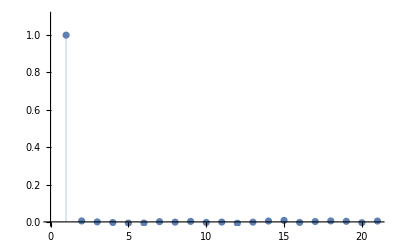

1.00076

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

```mathematica
(* Allan variance estimate *)
diffs=Most[l]-Rest[l];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.995126

0.99756

```mathematica
(* Convert to integers *)
lint=N@Round[l];
Mean[lint]
StandardDeviation[lint]
```

0.000137329

1.04185

```mathematica
(* Allan variance estimate *)
diffs=Most[lint]-Rest[lint];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

1.07893

1.03871

{1.,0.0059886,-0.000576386,-0.00312084,-0.00704296,-0.00442821,0.00179939,-0.000646679,0.00222111,-0.00432982,-0.00047799,-0.00591835,-0.00406272,0.00295211,0.00813943,-0.00282564,0.00366906,0.00248821,0.00189777,-0.00584806,0.00366906}

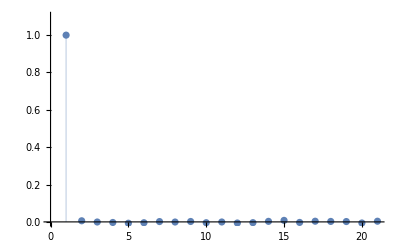

0.993547

```mathematica
cf=CorrelationFunction[N[lint],{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

0.

{a→25106.1,x0→-0.00608628,σ→1.04066}

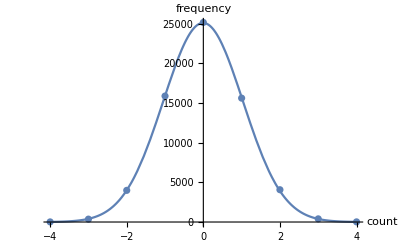

```mathematica
(* Distribution *)
ta=Tally[lint];
x0est=Sort[ta,#1[[2]]>#2[[2]]&][[1,1]]
p1=ListPlot[ta,AxesLabel->{"count","frequency"},LabelStyle->Larger];
fnc=a Exp[-(x-x0)^2/(2σ^2)];
sol=FindFit[ta,fnc,{{a,20000},{x0,x0est},{σ,1}},x]
fnc=fnc/.sol;
p2=Plot[fnc,{x,-4,4},PlotRange->All];
pp=Show[p1,p2]
```

0.999104

{1.,-0.00260952,0.00343592,-0.000470725,-0.00209111,0.00106623,0.000225582,0.000861662,-0.00308282,0.00148472,0.00481774,-0.00430234,-0.00101068,-0.00797402,-0.000109051,0.00158311,-0.0000806742,0.00354196,0.00387909,0.00559354,-0.00639747}

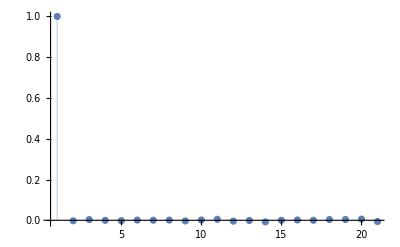

0.998361

```mathematica
(* LSB correlations *)
l2=Map[Mod[#,2]&,l];
Mean[l2]
cf=CorrelationFunction[l2,{20}]
ListPlot[cf,Filling->0,PlotRange->All]
Total[cf]
```